## Results - QED - Euler Method - Version 1

```mathematica
Z=Interpolation[Table[{xin+hx (i-1),z[[i]]},{i,m}]];
```

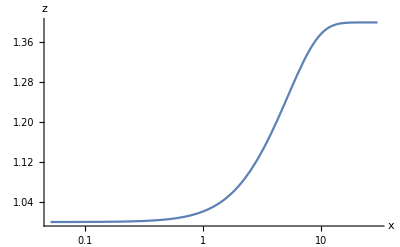

```mathematica
LogLinearPlot[Z[X],{X,xin,xfin},PlotRange->All,AxesLabel->{"x","z"}]
```

```mathematica
zmax=Max[z]
```

1.3997

#### Calculation of the Effective Number of Neutrino Species

```mathematica
(*Non-dimensional photon temperature*)
z0=(11/4.)^(1/3);
ργeq=π^2/15 z0^4;
ρνeq=7/8 π^2/15(me/xfin)^4;
ργ=π^2/15 zmax^4;
```

```mathematica
(*Exact energy densitiy for νe and νμ*)
ρνe=1/N[π]^2(me/xfin)^4 NIntegrate[ω^3 fν0[ω,zin],{ω,ymin,ymax}];
ρνμ=1/N[π]^2(me/xfin)^4 NIntegrate[ω^3 fν0[ω,zin],{ω,ymin,ymax}];
```

```mathematica
(*From Dolgov,1999*)
Neff=(ρνe+2ρνμ)/ρνeq ργeq/ργ
```

3.01164